```mathematica
Clear[rb]
bin2[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
rb[n_,k_,f_]:=rb[n,k,f]=Sum[f[j]rb[Floor[n/j],k-1,f],{j,2,n}]
rb[n_,0,f_]:=UnitStep[n-1]
lrb[n_,f_]:=Sum[(-1)^(k+1)/k rb[n,k,f],{k,1,Log2@n}]
rbz[n_,z_,f_]:=Sum[bin2[z,k]rb[n,k,f],{k,0,Log2@n}]
lrz[n_,z_,f_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,f],{k,0,Log2@n}]
id[n_]:=1
```

```mathematica
Limit[lrz[100,z,id],z->1]
```

99

```mathematica
Integrate[ lrz[100,z,id],{z,0,Infinity}]
```

$Aborted

$Aborted

```mathematica
D[x^z/z!,z]/.z->0
```

EulerGamma+Log[x]

```mathematica
D[Hypergeometric1F1[z,z+1,Log[x]]Log[x]^z/(z!),z]/.z->0
```

-Gamma[0,-Log[x]]-Log[-Log[x]]+Log[Log[x]]

```mathematica
D[FactorialPower[x,z]/z!,z]/.z->0
```

EulerGamma+PolyGamma[0,1+x]

```mathematica
Limit[D[lrz[100,z,id],z],z->0]
```

428/15

```mathematica
D[1/z!,z]/.z->0
```

EulerGamma

```mathematica
D[x^z,z]/.z->0
```

Log[x]

```mathematica
D[Hypergeometric1F1[z,z+1,Log[x]]Log[x]^z,z]/.z->0
```

-EulerGamma-Gamma[0,-Log[x]]-Log[-Log[x]]+Log[Log[x]]

```mathematica
D[FactorialPower[x,z],z]/.z->0
```

PolyGamma[0,1+x]

```mathematica
Limit[D[lrz[100,z,id]z!,z],z->0]
```

428/15-EulerGamma

```mathematica
Limit[D[z!,z],z->0]
```

-EulerGamma

```mathematica
FullSimplify[D[(x+z)!/x!/z!,z]/.z->0]
```

HarmonicNumber[x]

```mathematica
FullSimplify[D[(x+z)!/x!,z]/.z->0]
```

PolyGamma[0,1+x]

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
bin2[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
dzeta[j_,s_,z_]:=j^-s Product[(-1)^p[[2]]bin2[-z,p[[2]]],{p,FI[j]}]
dza[j_,z_]:=z! Product[(-1)^p[[2]]bin2[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[dzeta[j,s,z],{j,1,n}]
```

```mathematica
D[Expand[zeta[100,0,z]z!],z]/.z->0
```

428/15-EulerGamma

```mathematica
dza[4,z]
```

-1/2 (-1-z) z z!

```mathematica
D[-1/2 (-1-z) z z!,z]/.z->0
```

1/2

```mathematica
z!/.z->0
```

1

```mathematica
Integrate[Log[x]^(z-1)/(z-1)!,{x,1,n}]
```

ConditionalExpression[((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/((-1+z)!),Re[z]>0]

```mathematica
FullSimplify[((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/((-1+z)!)]
```

```mathematica
p1[n_,z_]:=((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/Gamma[z]
p1a[n_,z_]:=((Gamma[z,0,-Log[n]]) (-Log[n])^-z Log[n]^z)/Gamma[z]
p1b[n_,z_]:=(-1)^(-z)(Gamma[z,0,-Log[n]])/Gamma[z]
p1c[n_,z_]:=(-1)^(-z)(GammaRegularized[z,0,-Log[n]])
```

```mathematica
p2[n_,z_]:=Hypergeometric1F1[z,z+1,Log[n]] Log[n]^z/z!
```

```mathematica
p1c[33,2.7]
```

111.431+7.10543×10^-15 ⅈ

```mathematica
p2[33,2.7]
```

111.431

```mathematica
FullSimplify[(-1)^(-z)(Log[n])^-z Log[n]^z]
```

(-1)^-z

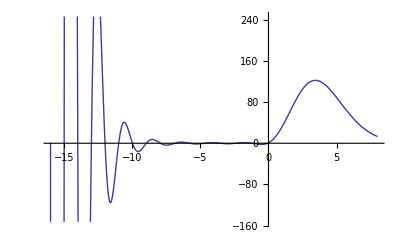

```mathematica
Plot[p1c[33,z],{z,-16,8}]
```

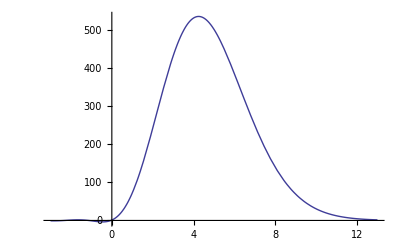

```mathematica
Plot[(-1)^(-z)GammaRegularized[z,0,-Log[73.]],{z,-3,13}]
```

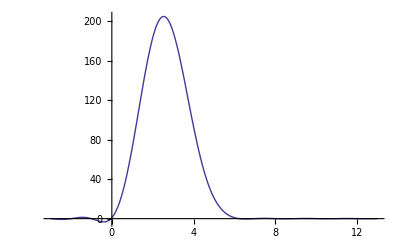

```mathematica
Plot[lrz[73.,z,id],{z,-3,13}]
```

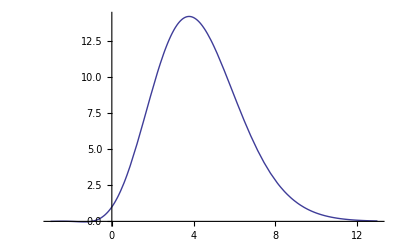

```mathematica
Plot[Log[73]^z/z!,{z,-3,13}]
```

```mathematica
Sum[Binomial[z,k]x^k,{k,0,Infinity}]
```

(1+x)^z

```mathematica
Sum[Binomial[z,k]Binomial[x,k],{k,0,Infinity}]
```

Gamma[1+x+z]/(Gamma[1+x] Gamma[1+z])

```mathematica
Integrate[lrz[20,2 E^(z I),id],{z,0,2Pi}]
```

2 π

```mathematica
N@E^(0 I)
```

1.

```mathematica
Integrate[E^(z I),{z,0,2Pi}]
```

0

```mathematica
FullSimplify@lrz[100,z,id]
```

((7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)+1/z) Sin[π z])/π

```mathematica
Series[((7/(-6+z)-51/(-5+z)+184/(-4+z)-324/(-3+z)+283/(-2+z)-99/(-1+z)+1/z) Sin[π z])/π,{z,0,20}]
```

1+(428 z)/15+1/450 (24568-75 π^2) z^2+((1974391-128400 π^2) z^3)/27000+(((137165317 π)/1620000-(6142 π^3)/675+π^5/120) z^4)/π+(((8876820679 π)/97200000-(1974391 π^3)/162000+(107 π^5)/450) z^5)/π+(((553927801273 π)/5832000000-(137165317 π^3)/9720000+(3071 π^5)/6750-π^7/5040) z^6)/π+(((33916558662151 π)/349920000000-(8876820679 π^3)/583200000+(1974391 π^5)/3240000-(107 π^7)/18900) z^7)/π+(((2056295769648937 π)/20995200000000-(553927801273 π^3)/34992000000+(137165317 π^5)/194400000-(3071 π^7)/283500+π^9/362880) z^8)/π+(((124035085696334119 π)/1259712000000000-(33916558662151 π^3)/2099520000000+(8876820679 π^5)/11664000000-(1974391 π^7)/136080000+(107 π^9)/1360800) z^9)/π+(((7462202539264212553 π)/75582720000000000-(2056295769648937 π^3)/125971200000000+(553927801273 π^5)/699840000000-(137165317 π^7)/8164800000+(3071 π^9)/20412000-π^11/39916800) z^10)/π+(((448342799392293597511 π)/4534963200000000000-(124035085696334119 π^3)/7558272000000000+(33916558662151 π^5)/41990400000000-(8876820679 π^7)/489888000000+(1974391 π^9)/9797760000-(107 π^11)/149688000) z^11)/π+(((26919044642424368873257 π)/272097792000000000000-(7462202539264212553 π^3)/453496320000000000+(2056295769648937 π^5)/2519424000000000-(79132543039 π^7)/4199040000000+(137165317 π^9)/587865600000-(3071 π^11)/2245320000+π^13/6227020800) z^12)/π+(((1615700166389595112025959 π)/16325867520000000000000-(448342799392293597511 π^3)/27209779200000000000+(124035085696334119 π^5)/151165440000000000-(33916558662151 π^7)/1763596800000000+(8876820679 π^9)/35271936000000-(1974391 π^11)/1077753600000+(107 π^13)/23351328000) z^13)/π+(((96958799007822681627514633 π)/979552051200000000000000-(26919044642424368873257 π^3)/1632586752000000000000+(7462202539264212553 π^5)/9069926400000000000-(2056295769648937 π^7)/105815808000000000+(79132543039 π^9)/302330880000000-(137165317 π^11)/64665216000000+(3071 π^13)/350269920000-π^15/1307674368000) z^14)/π+(((5818032908672660283778222471 π)/58773123072000000000000000-(1615700166389595112025959 π^3)/97955205120000000000000+(448342799392293597511 π^5)/544195584000000000000-(124035085696334119 π^7)/6348948480000000000+(33916558662151 π^9)/126978969600000000-(8876820679 π^11)/3879912960000000+(1974391 π^13)/168129561600000-(107 π^15)/4903778880000) z^15)/π+(((349097149662302744969059372777 π)/3526387384320000000000000000-(96958799007822681627514633 π^3)/5877312307200000000000000+(26919044642424368873257 π^5)/32651735040000000000000-(7462202539264212553 π^7)/380936908800000000000+(2056295769648937 π^9)/7618738176000000000-(7193867549 π^11)/3023308800000000+(137165317 π^13)/10087773696000000-(3071 π^15)/73556683200000+π^17/355687428096000) z^16)/π+(((20946284758123742763084523020199 π)/211583243059200000000000000000-(5818032908672660283778222471 π^3)/352638738432000000000000000+(1615700166389595112025959 π^5)/1959104102400000000000000-(448342799392293597511 π^7)/22856214528000000000000+(124035085696334119 π^9)/457124290560000000000-(3083323514741 π^11)/1269789696000000000+(8876820679 π^13)/605266421760000000-(1974391 π^15)/35307207936000000+(107 π^17)/1333827855360000) z^17)/π+(((1256790769354858960508851434445513 π)/12694994583552000000000000000000-(349097149662302744969059372777 π^3)/21158324305920000000000000000+(96958799007822681627514633 π^5)/117546246144000000000000000-(3845577806060624124751 π^7)/195910410240000000000000+(7462202539264212553 π^9)/27427457433600000000000-(2056295769648937 π^11)/838061199360000000000+(7193867549 π^13)/471636172800000000-(137165317 π^15)/2118432476160000000+(3071 π^17)/20007417830400000-π^19/121645100408832000) z^18)/π+(((75407856888133723986383774586393031 π)/761699675013120000000000000000000-(20946284758123742763084523020199 π^3)/1269499458355200000000000000000+(5818032908672660283778222471 π^5)/7052774768640000000000000000-(1615700166389595112025959 π^7)/82282372300800000000000000+(448342799392293597511 π^9)/1645647446016000000000000-(124035085696334119 π^11)/50283671961600000000000+(3083323514741 π^13)/198087192576000000000-(8876820679 π^15)/127105948569600000000+(1974391 π^17)/9603560558592000000-(107 π^19)/456169126533120000) z^19)/π+1/π((4524483739317223324740768655632419497 π)/45701980500787200000000000000000000-(1256790769354858960508851434445513 π^3)/76169967501312000000000000000000+(349097149662302744969059372777 π^5)/423166486118400000000000000000-(96958799007822681627514633 π^7)/4936942338048000000000000000+(3845577806060624124751 π^9)/14105549537280000000000000-(678382049024019323 π^11)/274274574336000000000000+(2056295769648937 π^13)/130737547100160000000000-(7193867549 π^15)/99043596288000000000+(137165317 π^17)/576213633515520000000-(3071 π^19)/6842536897996800000+π^21/51090942171709440000) z^20+O[z]^21

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z] Sum[ (-1)^k/(z -k)((x)^k)/k!,{k,0,Infinity}]]
```

x^z/Gamma[1+z]+(ExpIntegralE[1+z,x] Sin[π z])/π

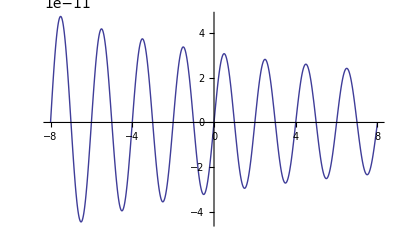

```mathematica
Plot[(ExpIntegralE[1+z,20.] Sin[π z])/π,{z,-8,8}]
```

```mathematica
FullSimplify@Expand[ Sum[ 1/(z-k )x^k/k!,{k,0,Infinity}]]
```

ExpIntegralE[1+z,-x]-(-x)^z Gamma[-z]

```mathematica
FullSimplify@Expand[ Sum[ (-1)^k/(k )((x)^k)/k!,{k,1,Infinity}]]
```

-EulerGamma-Gamma[0,x]-Log[x]

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z] Integrate[ (-1)^k/(z -k)((x)^k)/k!,{k,0,Infinity}]]
```

((∫_0^∞ ((-1)^k x^k)/((-k+z) k!)ⅆk) Sin[π z])/π

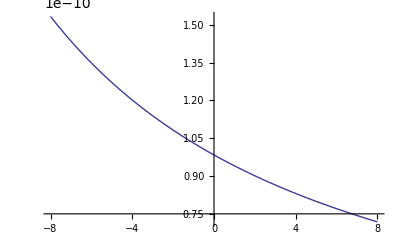

```mathematica
Plot[ExpIntegralE[1+z,20.] ,{z,-8,8}]
```

```mathematica
1.4+1.7+1.7
```

4.8

```mathematica
FullSimplify[1/Gamma[z]/Gamma[1-z]Sum[(-1)^k/(z-k)  Binomial[x,k],{k,0,Infinity}]]
```

Gamma[1+x]/(Gamma[1+x-z] Gamma[1+z])

```mathematica
FullSimplify@Series[Sin[Pi z]/Pi(-1)^k/(z-k)x^k/k!,{z,0,20}]
```

-((-1)^k x^k z)/(k^2 Gamma[k])-((-1)^k x^k z^2)/(k^3 Gamma[k])+((-1)^k (-6+k^2 π^2) x^k z^3)/(6 k^4 Gamma[k])+((-1)^k (-6+k^2 π^2) x^k z^4)/(6 k^5 Gamma[k])-(((-1)^k (120-20 k^2 π^2+k^4 π^4) x^k) z^5)/(120 (k^6 Gamma[k]))-(((-1)^k (120-20 k^2 π^2+k^4 π^4) x^k) z^6)/(120 (k^7 Gamma[k]))+((-1)^k (-5040+840 k^2 π^2-42 k^4 π^4+k^6 π^6) x^k z^7)/(5040 k^8 Gamma[k])+((-1)^k (-5040+840 k^2 π^2-42 k^4 π^4+k^6 π^6) x^k z^8)/(5040 k^9 Gamma[k])-(((-1)^k (362880-60480 k^2 π^2+3024 k^4 π^4-72 k^6 π^6+k^8 π^8) x^k) z^9)/(362880 (k^9 k!))-(((-1)^k (362880-60480 k^2 π^2+3024 k^4 π^4-72 k^6 π^6+k^8 π^8) x^k) z^10)/(362880 (k^11 Gamma[k]))+((-1)^k (-39916800+k^2 π^2 (6652800-332640 k^2 π^2+7920 k^4 π^4-110 k^6 π^6+k^8 π^8)) x^k z^11)/(39916800 k^12 Gamma[k])+((-1)^k (-39916800+k^2 π^2 (6652800-332640 k^2 π^2+7920 k^4 π^4-110 k^6 π^6+k^8 π^8)) x^k z^12)/(39916800 k^13 Gamma[k])-(((-1)^k (6227020800+k^2 π^2 (-1037836800+k^2 π^2 (51891840-1235520 k^2 π^2+17160 k^4 π^4-156 k^6 π^6+k^8 π^8))) x^k) z^13)/(6227020800 (k^14 Gamma[k]))-(((-1)^k (6227020800+k^2 π^2 (-1037836800+k^2 π^2 (51891840-1235520 k^2 π^2+17160 k^4 π^4-156 k^6 π^6+k^8 π^8))) x^k) z^14)/(6227020800 (k^15 Gamma[k]))+((-1)^k (-π/k^15+π^3/(6 k^13)-π^5/(120 k^11)+π^7/(5040 k^9)-π^9/(362880 k^7)+π^11/(39916800 k^5)-π^13/(6227020800 k^3)+π^15/(1307674368000 k)) x^k z^15)/(π k!)+((-1)^k (-1307674368000+k^2 π^2 (217945728000+k^2 π^2 (-10897286400+k^2 π^2 (259459200-3603600 k^2 π^2+32760 k^4 π^4-210 k^6 π^6+k^8 π^8)))) x^k z^16)/(1307674368000 k^17 Gamma[k])+((-1)^k (-π/k^17+π^3/(6 k^15)-π^5/(120 k^13)+π^7/(5040 k^11)-π^9/(362880 k^9)+π^11/(39916800 k^7)-π^13/(6227020800 k^5)+π^15/(1307674368000 k^3)-π^17/(355687428096000 k)) x^k z^17)/(π k!)-(((-1)^k (355687428096000+k^2 π^2 (-59281238016000+k^2 π^2 (2964061900800+k^2 π^2 (-70572902400+k^2 π^2 (980179200-8910720 k^2 π^2+57120 k^4 π^4-272 k^6 π^6+k^8 π^8))))) x^k) z^18)/(355687428096000 (k^19 Gamma[k]))+((-1)^k (-π/k^19+π^3/(6 k^17)-π^5/(120 k^15)+π^7/(5040 k^13)-π^9/(362880 k^11)+π^11/(39916800 k^9)-π^13/(6227020800 k^7)+π^15/(1307674368000 k^5)-π^17/(355687428096000 k^3)+π^19/(121645100408832000 k)) x^k z^19)/(π k!)+((-1)^k (-π/k^20+π^3/(6 k^18)-π^5/(120 k^16)+π^7/(5040 k^14)-π^9/(362880 k^12)+π^11/(39916800 k^10)-π^13/(6227020800 k^8)+π^15/(1307674368000 k^6)-π^17/(355687428096000 k^4)+π^19/(121645100408832000 k^2)) x^k z^20)/(π k!)+O[z]^21

```mathematica
Clear[pp,qq]
pp[n_,j_,k_,z_]:=pp[n,j,k,z]=If[n<j,0,1/(z-k)-pp[Floor[n/j],2,k+1,z]+pp[n,j+1,k,z]]
ppx[n_,z_]:=Sin[Pi z]/Pi  (1/z-pp[n,2,1,z])
ppz[n_,z_]:=Limit[ppx[n,z2],z2->z]
qq[n_,j_,k_,z_]:=qq[n,j,k,z]=If[n<j,0,1/(z-k)-qq[n-j,1,k+1,z]+qq[n,j+1,k,z]]
qqx[n_,z_]:=Sin[Pi z]/Pi  (1/z-qq[n,1,1,z])
qqz[n_,z_]:=Limit[qqx[n,z2],z2->z]
```

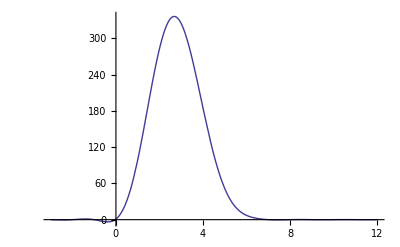

```mathematica
Plot[ppx[100,z],{z,-3,12}]
```

```mathematica
qqx[9,z]
```

((-1/(-9+z)+9/(-8+z)-36/(-7+z)+84/(-6+z)-126/(-5+z)+126/(-4+z)-84/(-3+z)+36/(-2+z)-9/(-1+z)+1/z) Sin[π z])/π

```mathematica
ppz[100,1/2]
```

113678/(1155 π)

```mathematica
Limit[D[ppx[100,z],z],z->0]
```

428/15

```mathematica
Sum[(-1)^k/(z-k)x^k,{k,0,Infinity}]
```

-HurwitzLerchPhi[-x,1,-z]

```mathematica
Sum[(-1)^n/(a-n)z^n,{n,0,Infinity}]
```

-HurwitzLerchPhi[-z,1,-a]

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z]Sum[(-1)^k/(z-k)x^k/Gamma[k+1],{k,0,Infinity}]]
```

x^z/Gamma[1+z]+(ExpIntegralE[1+z,x] Sin[π z])/π

```mathematica
Gamma[1-z]/.z->.3
```

1.29806

```mathematica
Gamma[-z](-z)/.z->.3
```

1.29806

```mathematica
(x^z Gamma[1-z])/z+x^z Gamma[-z,x]/.z->.3/.x->1.4
```

4.89096+5.98969×10^-16 ⅈ

```mathematica
-x^z Gamma[-z]+x^z Gamma[-z,x]/.z->.3/.x->1.4
```

4.89096+5.98969×10^-16 ⅈ

```mathematica
-x^z Gamma[-z,0, x]/.z->.3/.x->1.4
```

4.89096+5.98969×10^-16 ⅈ

```mathematica
Expand@FullSimplify@Expand[(-x^z Gamma[-z]+x^z Gamma[-z,x])/Gamma[z]/Gamma[1-z]]
```

(ExpIntegralE[1+z,x] Sin[π z])/π-(x^z Gamma[-z] Sin[π z])/π

```mathematica
D[x^z/Gamma[1+z]+(ExpIntegralE[1+z,x] Sin[π z])/π,z]/.z->0
```

EulerGamma+ExpIntegralE[1,x]+Log[x]

```mathematica
Sin[.5  Pi]/Pi Sum[(-1)^k/(.5-k)10.^k/Gamma[k+1],{k,0,Infinity}]
```

3.56825

```mathematica
10^.5/(.5)!
```

3.56825

```mathematica
D[x^z/z!,z]/.z->0
```

EulerGamma+Log[x]

```mathematica
D[Binomial[x,z],z]/.z->0
```

EulerGamma+PolyGamma[0,1+x]

```mathematica
D[x^z,z]/.z->0
```

Log[x]

```mathematica
D[Binomial[x,z]z!,z]/.z->0
```

PolyGamma[0,1+x]

```mathematica
Expand@FullSimplify[ppx[100,z]/(Sin[Pi z]/Pi)Product[(z-k),{k,0,6}]]/.z->2
```

13584

```mathematica
po[n_]:=List@@NRoots[Expand@FullSimplify[ppx[n,z]/(Sin[Pi z]/Pi)Product[z-k,{k,0,Log2@n}]]==0,z][[All,2]]
```

```mathematica
Limit[FullSimplify[Expand[6! Product[1-z/r,{r,po[100]}]/Product[z-k,{k,0,6}] Sin[Pi z]/Pi]],z->2]
```

283.+0. ⅈ

```mathematica
Limit[FullSimplify[Expand[6! Product[1-z/r,{r,po[100]}]/Product[z-k,{k,0,6}] Sin[Pi z]/Pi]],z->3]
```

324.+0. ⅈ

```mathematica
Sum[-1/r,{r,po[100]}]
```

26.0833+0. ⅈ

```mathematica
pps[n_,j_,k_,z_,s_]:=pps[n,j,k,z,s]=If[n<j,0,j^-s(1/(z-k)-pps[Floor[n/j],2,k+1,z,s])+pps[n,j+1,k,z,s]]
ppsx[n_,z_,s_]:=Sin[Pi z]/Pi  (1/z-pps[n,2,1,z,s])
ppsz[n_,z_,s_]:=Limit[ppsx[n,z2,s],z2->z]
```

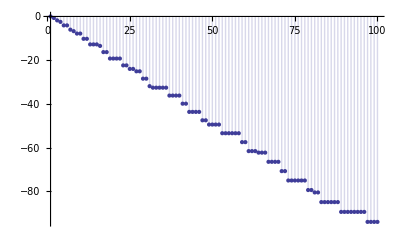

```mathematica
DiscretePlot[N[D[D[ppsx[n,z,s],s]/.s->0,z]/.z->0],{n,1,100}]
```

```mathematica
FullSimplify[1/(z-2)/Gamma[z]/Gamma[1-z]]
```

Sin[π z]/(π (-2+z))

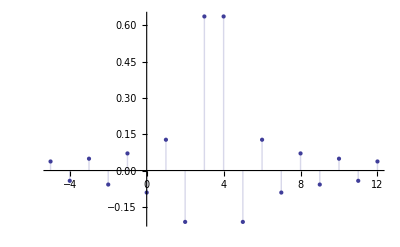

```mathematica
DiscretePlot[Re[(-1)^k Sin[Pi z]/Pi /(z-k)]/.z->3.5,{k,-5,12}]
```

```mathematica
Sum[1/Gamma[z]/Gamma[1-z](-1)^k/(z-k)x^k/k!,{k,-1000,Infinity}]
```

(x^z (Gamma[1-z]+z Gamma[-z,x]))/(z Gamma[1-z] Gamma[z])

```mathematica
Table[Limit[Sin[Pi -3]/Pi(-1)^k/(-3-k)x^k/k!,k->k2],{k2,-15,15}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,(2 Sin[3])/(π x^3),0,0,-Sin[3]/(3 π),(x Sin[3])/(4 π),-(x^2 Sin[3])/(10 π),(x^3 Sin[3])/(36 π),-(x^4 Sin[3])/(168 π),(x^5 Sin[3])/(960 π),-(x^6 Sin[3])/(6480 π),(x^7 Sin[3])/(50400 π),-(x^8 Sin[3])/(443520 π),(x^9 Sin[3])/(4354560 π),-(x^10 Sin[3])/(47174400 π),(x^11 Sin[3])/(558835200 π),-(x^12 Sin[3])/(7185024000 π),(x^13 Sin[3])/(99632332800 π),-(x^14 Sin[3])/(1482030950400 π),(x^15 Sin[3])/(23538138624000 π)}

```mathematica
(-3)!
```

ComplexInfinity

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z]Sum[(-1)^k/(z-k)1/k!,{k,0,Infinity}]]
```

1/Gamma[1+z]+(ExpIntegralE[1+z,1] Sin[π z])/π

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z]Sum[(-1)^k/(z-k)Pochhammer[x,k]/k!,{k,0,Infinity}]]
```

(Hypergeometric2F1[x,-z,1-z,-1] Sin[π z])/(π z)

```mathematica
(Hypergeometric2F1[x,-z,1-z,-1] Sin[π z])/(π z)/.x->7./.z->3.3
```

112.366

```mathematica
Pochhammer[7,3.3]/(3.3)!
```

112.366

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z]Sum[(-1)^k/(z-k)Binomial[x,k],{k,0,Infinity}]]
```

Gamma[1+x]/(Gamma[1+x-z] Gamma[1+z])

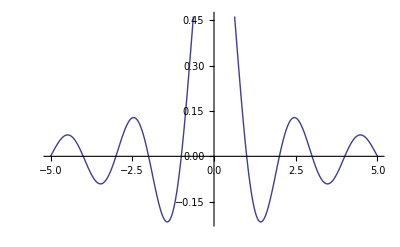

```mathematica
Plot[Sin[Pi z]/(Pi (z)),{z,-5,5}]
```

```mathematica
Plot[Binomial[0,z],{z,-5,5}]
```

-Graphics-

```mathematica
FactorialPower[x,3]/.x->5
```

60

```mathematica
5 4 3
```

60

```mathematica
Expand[1/Gamma[z]/Gamma[1-z] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]/.x->n
```

n^z/(z Gamma[z])+(n^z Gamma[-z,n])/(Gamma[1-z] Gamma[z])

```mathematica
Plot[(ExpIntegralE[1+z,12] Sin[π z])/π,{z,-130,-128}]
```

-Graphics-

```mathematica
(n^z Gamma[-z,n])/(Gamma[1-z] Gamma[z])/.n->-3.3/.z->1.3
```

3.11237+3.27388 ⅈ

```mathematica
-(n^z Gamma[-z,n])/(Gamma[-z] Gamma[z+1])/.n->-3.3/.z->1.3
```

3.11237+3.27388 ⅈ

```mathematica
-(n^z GammaRegularized[-z,n])/Gamma[z+1]/.n->-3.3/.z->1.3
```

3.11237+3.27388 ⅈ

```mathematica
n^z/(z Gamma[z])+(n^z Gamma[-z,n])/(Gamma[1-z] Gamma[z])/.n->13.3/.z->1.3
```

24.7767

```mathematica
n^z/Gamma[z+1](1-GammaRegularized[-z,n])/.n->13.3/.z->1.3
```

24.7767

```mathematica
n^z/Gamma[z+1](GammaRegularized[-z,0,n])/.n->13.3/.z->1.3
```

24.7767

```mathematica
FullSimplify[1/Gamma[z]/Gamma[1-z]/GammaRegularized[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

-(x^z Gamma[-z] Sin[π z])/π

```mathematica
17^(5/3)/Gamma[5/3+1]
```

(17 17^(2/3))/Gamma[8/3]

```mathematica
FullSimplify[Gamma[-z]/Gamma[z]/z/Gamma[-z]/Gamma[-z,0,x]]
```

1/(z Gamma[z] Gamma[-z,0,x])

```mathematica
-(x^z Gamma[-z] Sin[π z])/π/.x->12.3/.z->2.2
```

103.101

```mathematica
12.3^2.2/(2.2!)
```

103.101

```mathematica
FullSimplify[z Gamma[z] Gamma[-z,0,x]]
```

z Gamma[z] Gamma[-z,0,x]

```mathematica
FullSimplify[-1/Gamma[z+1]/Gamma[-z,0,x]/GammaRegularized[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

x^z/(Gamma[1+z] GammaRegularized[-z,0,x])

```mathematica
x^z/(Gamma[1+z] GammaRegularized[-z,0,x])/.x->12.3/.z->2.2
```

103.101

```mathematica
-(x^z Gamma[-z] Sin[π z])/π/.z->-40.2/.x->62.3
```

5.79129×10^-27

```mathematica
FullSimplify@Expand[1/Gamma[z]/Gamma[1-z]/GammaRegularized[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

-(x^z Gamma[-z] Sin[π z])/π

```mathematica
Limit[-(Gamma[-z] Sin[π z])/π,z->1/2]
```

2/(√π)

```mathematica
1/(1/2)!
```

2/(√π)

```mathematica
FullSimplify@Expand[Gamma[-z]/Gamma[z]/Gamma[-z]/-z/Gamma[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

x^z/Gamma[1+z]

```mathematica
FullSimplify@Expand[1/Gamma[z]/-z/Gamma[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

x^z/Gamma[1+z]

```mathematica
FullSimplify@Expand[-1/(Gamma[1+z] Gamma[-z,0,x]) Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]
```

x^z/Gamma[1+z]

```mathematica
FullSimplify[Sin[Pi z]/Pi/GammaRegularized[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]/.x->13.3/.z->4.2
```

1611.58

```mathematica
FullSimplify@Expand[-1/z!/( Gamma[-z,0,x]) Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]]/.x->13.3/.z->4.2
```

1611.58

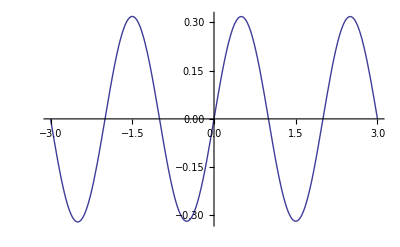

```mathematica
Plot[ -1/z!/Gamma[-z,0,8.],{z,-3,3}]
```

```mathematica
Plot[ Sin[Pi z]/Pi/GammaRegularized[-z,0,8.],{z,-3,3}]
```

-Graphics-

```mathematica
FullSimplify@Table[(-1)^k/(z-k) 17.^k/k!,{k,0,55}]
```

{1./z,-17./(-1.+z),144.5/(-2.+z),-818.833/(-3.+z),3480.04/(-4.+z),-11832.1/(-5.+z),33524.4/(-6.+z),-81416.4/(-7.+z),173010./(-8.+z),-326796./(-9.+z),555554./(-10.+z),-858583./(-11.+z),(1.21633×10^6)/(-12.+z),-(1.59058×10^6)/(-13.+z),(1.93142×10^6)/(-14.+z),-(2.18894×10^6)/(-15.+z),(2.32575×10^6)/(-16.+z),-(2.32575×10^6)/(-17.+z),(2.19654×10^6)/(-18.+z),-(1.96533×10^6)/(-19.+z),(1.67053×10^6)/(-20.+z),-(1.35233×10^6)/(-21.+z),(1.04498×10^6)/(-22.+z),-772380./(-23.+z),547102./(-24.+z),-372029./(-25.+z),243250./(-26.+z),-153157./(-27.+z),92988.4/(-28.+z),-54510.5/(-29.+z),30889.3/(-30.+z),-16939.3/(-31.+z),8998.99/(-32.+z),-4635.84/(-33.+z),2317.92/(-34.+z),-1125.85/(-35.+z),531.65/(-36.+z),-244.272/(-37.+z),109.279/(-38.+z),-47.6346/(-39.+z),20.2447/(-40.+z),-8.39415/(-41.+z),3.39763/(-42.+z),-1.34325/(-43.+z),0.518983/(-44.+z),-0.19606/(-45.+z),0.0724571/(-46.+z),-0.0262079/(-47.+z),0.00928195/(-48.+z),-0.00322027/(-49.+z),0.00109489/(-50.+z),-0.000364964/(-51.+z),0.000119315/(-52.+z),-0.0000382709/(-53.+z),0.0000120482/(-54.+z),-(3.724×10^-6)/(-55.+z)}

```mathematica
-1/Gamma[-1/2,0,17.]
```

0.282095

```mathematica
Integrate[ Log[x]^(z-1)/(z-1)!,{x,1,n}]
```

ConditionalExpression[((Gamma[z]-Gamma[z,-Log[n]]) (-Log[n])^-z Log[n]^z)/((-1+z)!),Re[z]>0]

```mathematica
FullSimplify[(GammaRegularized[z,0,-Log[n]]) (-1)^-z (Log[n])^-z Log[n]^z]
```

(-1)^-z GammaRegularized[z,0,-Log[n]]

```mathematica
N[(-1)^-z GammaRegularized[z,0,-Log[n]]/.n->100/.z->2.5]
```

532.148+0. ⅈ

```mathematica
Hypergeometric1F1[z,z+1,Log[n]]Log[n]^z/z!/.n->100./.z->2.5
```

532.148+3.22168×10^-17 ⅈ

```mathematica
N[(-1)^-z GammaRegularized[z,0,-n]/.n->3./.z->2.5]
```

47.5073+0. ⅈ

```mathematica
n^z/z!/.n->3./.z->2.5
```

4.69058

```mathematica
Sin[Pi z]/Pi/GammaRegularized[-z,0,x] Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}]/.x->13.3/.z->4.2
```

1611.58

```mathematica
x^z/z!/.x->13.3/.z->4.2
```

1611.58

```mathematica
bb[x_,z_]:=Sin[Pi z]/Pi/GammaRegularized[z,0,x] Sum[ (-1)^k/(z-k)Hypergeometric1F1[k,k+1,Log[x]]Log[x]^k/k!,{k,0,80}]
bb2[x_,z_]:=(-1)^-z GammaRegularized[z,0,-Log[x]]
```

```mathematica
bb[131.1,7.2]
```

961.377

```mathematica
bb2[131.1,7.2]
```

961.298+5.68434×10^-14 ⅈ

```mathematica
Expand[Sum[ 1/Gamma[z]/Gamma[1-z] (-1)^k/(z-k)Hypergeometric1F1[k,k+1,Log[x]]Log[x]^k/k!,{k,0,Infinity}]]
```

∑_(k=0)^∞ ((-1)^k (Gamma[1+k]-k Gamma[k,-Log[x]]) (-Log[x])^-k Log[x]^k)/((-k+z) k! Gamma[1-z] Gamma[z])

```mathematica
D[-1/(Gamma[1+z] Gamma[-z,0,x]) Sum[ (-1)^k/(z-k)x^k/(k!),{k,0,Infinity}],x]
```

(ⅇ^-x (Gamma[1-z]+z Gamma[-z,x]))/(x z Gamma[1+z] Gamma[-z,0,x]^2)+ⅇ^-x/(x Gamma[1+z] Gamma[-z,0,x])-(x^(-1+z) (Gamma[1-z]+z Gamma[-z,x]))/(Gamma[1+z] Gamma[-z,0,x])

```mathematica
Integrate[(ⅇ^-x (Gamma[1-z]+z Gamma[-z,x]))/(x z Gamma[1+z] Gamma[-z,0,x]^2)+ⅇ^-x/(x Gamma[1+z] Gamma[-z,0,x])-(x^(-1+z) (Gamma[1-z]+z Gamma[-z,x]))/(Gamma[1+z] Gamma[-z,0,x]),x]
```

-(x^z (Gamma[1-z]+z Gamma[-z,x]))/(z Gamma[1+z] (Gamma[-z]-Gamma[-z,x]))

```mathematica
D[-1/z!/Gamma[-z,0,x]Sum[(-1)^k/(z-k) x^k/k!,{k,0,Infinity}],x]/.x->13.3/.z->3.2
```

122.447

```mathematica
x^(z-1)/(z-1)!/.x->13.3/.z->3.2
```

122.447

```mathematica
1/Gamma[z]/Gamma[1-z]/.z->13.3
```

-0.257518

```mathematica
1/Gamma[z+1]/Gamma[-z]/(-1)/.z->13.3
```

-0.257518

```mathematica
Gamma[-3.3]
```

0.438517

```mathematica
Gamma[-3.3]
```

0.438517

```mathematica
Sum[Gamma[k,0,-Log[x]]/Gamma[k]/(z-k),{k,0,Infinity}]
```

∑_(k=0)^∞ Gamma[k,0,-Log[x]]/((-k+z) Gamma[k])

```mathematica
Integrate[ 1,{x,1,n}]
```

-1+n

```mathematica
Expand@Integrate[1,{x,1,n},{y,1,n/x}]
```

ConditionalExpression[1-n+n Log[n],Re[n]≥0||n∉Reals]

```mathematica
Expand@Integrate[1,{x,1,n},{y,1,n/x},{z,1,n/(x y)}]
```

ConditionalExpression[-1+n-n Log[n]+1/2 n Log[n]^2,Re[n]≥0||n∉Reals]

```mathematica
-1+n-n Log[n]+1/2 n Log[n]^2/.n->13.3
```

22.4146

```mathematica
(-1)^(-3)GammaRegularized[3,0,-Log[13.3]]
```

22.4146-8.235×10^-15 ⅈ

```mathematica
pk[x_,k_]:=1-x Sum[(-Log[x])^j/j!,{j,0,k-1}]
```

```mathematica
Expand@pk[n,4]
```

1-n+n Log[n]-1/2 n Log[n]^2+1/6 n Log[n]^3

```mathematica
Gamma[k,0,-Log[x]]/Gamma[k]/.x->13./.k->4
```

15.1429-7.4179×10^-15 ⅈ

```mathematica
Table[Expand[pk[n,k]/(z-k)],{k,0,5}]//TableForm
```

1/z
1/(-1+z)-n/(-1+z)
1/(-2+z)-n/(-2+z)+(n Log[n])/(-2+z)
1/(-3+z)-n/(-3+z)+(n Log[n])/(-3+z)-(n Log[n]^2)/(2 (-3+z))
1/(-4+z)-n/(-4+z)+(n Log[n])/(-4+z)-(n Log[n]^2)/(2 (-4+z))+(n Log[n]^3)/(6 (-4+z))
1/(-5+z)-n/(-5+z)+(n Log[n])/(-5+z)-(n Log[n]^2)/(2 (-5+z))+(n Log[n]^3)/(6 (-5+z))-(n Log[n]^4)/(24 (-5+z))

```mathematica
FullSimplify@Sum[pk[n,k]/(z-k),{k,0,Infinity}]
```

∑_(k=0)^∞ (1-Gamma[k,-Log[n]]/Gamma[k])/(-k+z)

```mathematica
((-1)^(-z)Gamma[z,0,-Log[x]]/Gamma[z])/Sum[(-1)^k/(z-k) (-1)^(-k)Gamma[k,0,-Log[x]]/Gamma[k],{k,0,Infinity}]
```

((-1)^-z Gamma[z,0,-Log[x]])/(Gamma[z] ∑_(k=0)^∞ Gamma[k,0,-Log[x]]/((-k+z) Gamma[k]))